# Cosmology: Problem Set 5

```mathematica
<<NumericalCalculus`;(*Load Package for Finding Limits Numerically*)
```

```mathematica
vMap = ResourceFunction["ViridisColor"];
```

## Problem 1

```mathematica
params = {τ->1.4*^18, Q->1.3*^6,G->6.7087*^-57, g->10};
```

```mathematica
H = Sqrt[(8π G)/3×π^2/30 g] Q^2/x^2;
```

```mathematica
Γ = 3060/τ 1/x^5(1+x/2+x^2/12);
```

```mathematica
ode = (D[f[x],x]==-Γ/(H x)(f[x]- (1-f[x])Exp[-x]))/.params
```

f'[x]==-(3.00773 (1+x/2+x^2/12) (-ⅇ^-x (1-f[x])+f[x]))/x^4

```mathematica
x0 = 0.01;
xF = 100.0;
sol = NDSolveValue[{ode, f[x0]==0.5},f, {x,x0,xF}]
```

InterpolatingFunction[…]

```mathematica
ϵ = 1*^-6;
solLim= NLimit[sol[x], x->(xF-ϵ), Direction->xF]
```

0.149533

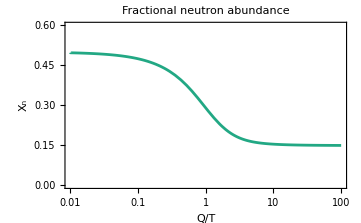

```mathematica
Plot[sol[x],{x,x0,xF},
ScalingFunctions->{"Log"}, 
PlotLabel->"Fractional neutron abundance",
PlotStyle->vMap[0.6], 
Frame->True, 
FrameLabel->{"Q/T", "X_n"},
PlotRange->{{0,0.6}}]
```

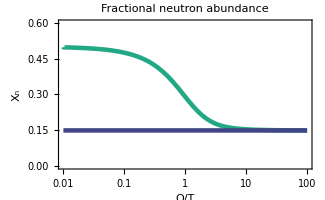

```mathematica
Plot[{sol[x], solLim},{x,x0,xF},
ScalingFunctions->{"Log"}, 
PlotLabel->"Fractional neutron abundance",
PlotStyle->{{Thickness[0.01],vMap[0.6]}, {Thickness[0.01],vMap[0.2]}}, 
Frame->True, 
FrameLabel->{"Q/T", "X_n"},
PlotRange->{{0,0.6}}]
```

## Problem 2:

```mathematica
solX = DSolve[(1-χ[T])/χ[T]^2==χ0 η ((2π T)/Subscript[m, e])^(3/2)Exp[EI/T],χ[T],T, Assumptions->{Subscript[m, e]->PositiveReals}]
```

{{χ[T]→-(ⅇ^(-EI/T) (1-√(1+8 √2 ⅇ^(EI/T) π^(3/2) η χ0 (T/m_e)^(3/2))))/(4 √2 π^(3/2) η χ0 (T/m_e)^(3/2))},{χ[T]→-(ⅇ^(-EI/T) (1+√(1+8 √2 ⅇ^(EI/T) π^(3/2) η χ0 (T/m_e)^(3/2))))/(4 √2 π^(3/2) η χ0 (T/m_e)^(3/2))}}

```mathematica
χSol1 = χ[T]/.solX[[1]]
```

-(ⅇ^(-EI/T) (1-√(1+8 √2 ⅇ^(EI/T) π^(3/2) η χ0 (T/m_e)^(3/2))))/(4 √2 π^(3/2) η χ0 (T/m_e)^(3/2))

```mathematica
χSol1//TeXForm (*Get String for LaTeX document*)
```

-\frac{e^{-\frac{\text{EI}}{T}} \left(1-\sqrt{8 \sqrt{2} \pi
   ^{3/2} \eta  \text{$\chi $0} e^{\text{EI}/T}
   \left(\frac{T}{m_e}\right){}^{3/2}+1}\right)}{4 \sqrt{2} \pi
   ^{3/2} \eta  \text{$\chi $0}
   \left(\frac{T}{m_e}\right){}^{3/2}}